## Пример 1. Реализация алгоритма.

### 1.1. Инициализация. Функции нахождения входа и выходов.

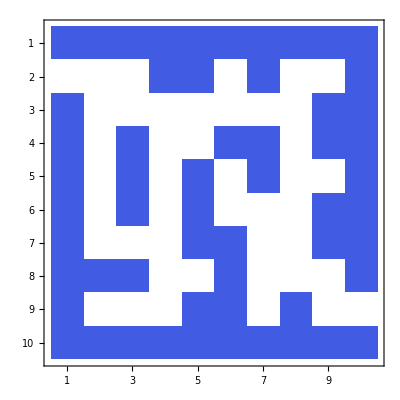

```mathematica
labyrinth={{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{0,0,0,-1,-1,0,-1,0,0,-1},
{-1,0,0,0,0,0,0,0,-1,-1},
{-1,0,-1,0,0,-1,-1,0,-1,-1},
{-1,0,-1,0,-1,0,-1,0,0,-1},
{-1,0,-1,0,-1,0,0,0,-1,-1},
{-1,0,0,0,-1,-1,0,0,-1,-1},
{-1,-1,-1,0,0,-1,0,0,0,-1},
{-1,0,0,0,-1,-1,0,-1,0,0},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}};
MatrixPlot[labyrinth]
```

```mathematica
findEnterance[labyrinth_]:=Flatten[{FirstPosition[labyrinth⟦;;,1⟧,0],1}]
findExit[labyrinth_]:=Flatten[{FirstPosition[labyrinth⟦;;,Length[labyrinth]⟧,0],Length[labyrinth]}]
findEnterance[labyrinth];
findExit[labyrinth];
```

### 1.2. Реализация волнового алгоритма(алгоритма Ли).

Функции нахождения соседних доступных точек.

```mathematica
findNeighbour[labyrinth_,point_]:=Module[{row=point//First,col=point//Last,res={}},
If[(row+1≤ Length[labyrinth])&&labyrinth[[row+1,col]]==0,res=Append[res,{row+1,col}]];
If[(col+1≤ Length[labyrinth⟦1⟧])&&labyrinth[[row,col+1]]==0,res=Append[res,{row,col+1}]];
If[(row-1>0)&&labyrinth[[row-1,col]]==0,res=Append[res,{row-1,col}]];
If[(col-1>0)&&labyrinth[[row,col-1]]==0,res=Append[res,{row,col-1}]];
res
]
findNeighbours[labyrinth_,points_]:=Module[{res={}},
Flatten[findNeighbour[labyrinth,#]&/@points,1]
]
```

Волновой алгоритм(создание сетки от стартовой точки(входа) до конца(выхода)).

```mathematica
makeGrid[labyrinth_,st_,end_]:=Module[{res=labyrinth,toPin,value=1},
res=ReplacePart[res,st->value];
value++;
toPin=findNeighbour[res,st];
While[Length[Position[toPin,end]]==0,
res=ReplacePart[res,toPin-> value];
value++;
toPin=findNeighbours[res,toPin];
toPin=DeleteDuplicates[toPin];
];
res=ReplacePart[res,end->value];
res
]
```

Волновой алгоритм (создание сетки от стартовой точки по всем другим точкам, которые не являются стенами).[Необходим для алгоритма №2]

```mathematica
makeFullGrid[labyrinth_,st_]:=Module[{res=labyrinth,toPin,value=0},
res=ReplacePart[res,st->value];
value++;
toPin=findNeighbour[res,st];
While[Length[Position[res,0]]≠ 0,
res=ReplacePart[res,toPin-> value];
value++;
toPin=findNeighbours[res,toPin];
toPin=DeleteDuplicates[toPin];
];
res
]
```

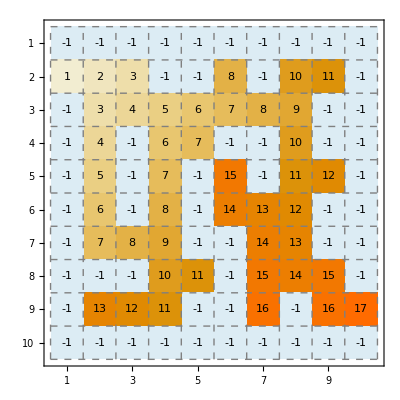

```mathematica
myGridForLyb=makeGrid[labyrinth,{2,1},{9,10}];
MatrixPlot[%,Mesh->All,MeshStyle->Directive[Gray,Dashed],Epilog->MapIndexed[Text[#1,Reverse[{Abs[10.5-#2⟦1⟧],#2⟦2⟧-.5}]]&,myGridForLyb,{2}]]
```

### 1.3. Поиск пути.

Выбор точки перехода.

```mathematica
findBest[grid_,point_]:=Module[{row=point//First,col=point//Last,scoreOfDesirePoint=Extract[grid,point]-1},
If[(col+1≤ Length[grid⟦1⟧])&&grid[[row,col+1]]==scoreOfDesirePoint,Return[{row,col+1}]];
If[(col-1>0)&&grid[[row,col-1]]==scoreOfDesirePoint,Return[{row,col-1}]];
If[(row+1≤ Length[grid])&&grid[[row+1,col]]==scoreOfDesirePoint,Return[{row+1,col}]];
If[(row-1>0)&&grid[[row-1,col]]==scoreOfDesirePoint,Return[{row-1,col}]];
]
```

Функция поиска пути.

```mathematica
findPath[grid_,st_,end_]:=Module[{res},
res={end,findBest[grid,end]};
While[(res//Last)≠st,
res=Append[res,findBest[grid,res//Last]]
];
res
]
```

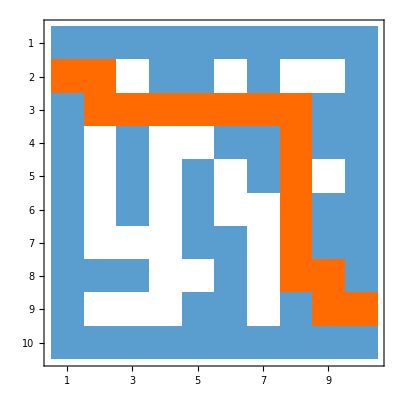

```mathematica
solution=findPath[makeGrid[labyrinth,{2,1},{9,10}],{2,1},{9,10}];
ReplacePart[labyrinth,solution->10];
MatrixPlot[%]
```

```mathematica
Manipulate[MatrixPlot[ReplacePart[myGridForLyb,(solution)⟦1;;a⟧->100],ColorRules->{100->Purple},Epilog->MapIndexed[Text[#1,Reverse[{Abs[10.5-#2⟦1⟧],#2⟦2⟧-.5}]]&,myGridForLyb,{2}]],{a,1,Length[solution],1}]
```

Вспомогательная функция для экспортирования анимации.

```mathematica
save1[t_]:=MatrixPlot[ReplacePart[myGridForLyb,(solution)⟦1;;t⟧->100],ColorRules->{100->Purple},Epilog->MapIndexed[Text[#1,Reverse[{Abs[10.5-#2⟦1⟧],#2⟦2⟧-.5}]]&,myGridForLyb,{2}]]
(**Export["C:\\Users\\FullSpace\\Desktop\\courseWork\\solution1gif\\"<>ToString[#]<>".png",save1[#]]&/@Range[1,Length[solution]];**)
```

### 1.4 Первый алгоритм

```mathematica
firstAlgorithm[labyrinth_]:=findPath[makeGrid[labyrinth,findEnterance[labyrinth],findExit[labyrinth]],findEnterance[labyrinth],findExit[labyrinth]]
firstAlgorithm[labyrinth];
```

В дальнейшем понадобится алгоритм нахождения кратчайшего пути из точки a в точку b, поэтому зададим ещё один алгоритм.

```mathematica
firstAlgorithm[labyrinth_,st_,end_]:=findPath[makeGrid[labyrinth,st,end],st,end]
```

## Пример 2. Реализация алгоритма. Добавление “еды”.

```mathematica
enterance1={2,1};
```

```mathematica
numberOfTreats = 10;
Treats = RandomSample[DeleteCases[Position[labyrinth, 0],enterance1], numberOfTreats];
Pheramones = Table[.5, {i, 1, numberOfTreats+1}, {j, 1, numberOfTreats+1}];
Treats=Prepend[Treats,enterance1];
```

```mathematica
CreateGraphForTreat[labyrinth_,numberOfTreats_,Treats_,closenessconst_]:=Block[{TreatsDistancesRelatively,tempGrid,TreatsDistances},
TreatsDistancesRelatively=Table[0,{i,1,numberOfTreats},{j,1,numberOfTreats}];
TreatsDistances=Table[0,{i,1,numberOfTreats},{j,1,numberOfTreats}];
For[i=1,i≤ numberOfTreats,i++,
tempGrid=makeFullGrid[labyrinth,Treats⟦i⟧];
TreatsDistances⟦i⟧=Extract[tempGrid,Treats];
TreatsDistancesRelatively⟦i⟧=closenessconst/Extract[tempGrid,Treats];
];
{TreatsDistancesRelatively,TreatsDistances}
]
```

```mathematica
TreatsDistancesRelatively=CreateGraphForTreat[labyrinth,numberOfTreats+1,Treats,10];
TreatsDistances=TreatsDistancesRelatively//Last;
TreatsDistancesRelatively=TreatsDistancesRelatively//First;
```

```mathematica
a=1;(**можно сказать увеличивает зависимость выбора от дистанции**)
b=1;(**можно сказать увеличивает зависимость выбора от ферамонов**)
Q=20;(**константа при добавлении феромонов**)
p=.4;(**коэф испарения**)
numberOfGoldDiggers=1;(**amount of ants**)
```

```mathematica
CreatePath[Treats_,TreatsDistancesRelatively_,Pheramones_,a_,b_]:=Block[{path={1},leftPoints,leftDistance,leftPheramones,allCriterias,probability,choosedPoint},
While[Length[path]≠ numberOfTreats +1,
leftPoints=Flatten[Position[Treats,Alternatives@@Delete[Treats,Partition[path,1]]]];
leftDistance=Extract[TreatsDistancesRelatively,{path//Last,#}]&/@leftPoints;
leftPheramones=Extract[Pheramones,{path//Last,#}]&/@leftPoints;
allCriterias=(leftDistance^a*leftPheramones^b)//Total;
probability=(leftDistance^a*leftPheramones^b)/allCriterias;
choosedPoint=RandomChoice[probability-> leftPoints];
path=Append[path,choosedPoint];
];
path
]
CreatePath[Treats,TreatsDistancesRelatively,Pheramones,a,b];
```

```mathematica
CreatePaths[Treats_,TreatsDistancesRelatively_,Pheramones_,a_,b_,numOfAnts_]:=Block[{res={}},
Table[CreatePath[Treats,TreatsDistancesRelatively,Pheramones,a,b],{j,1,numOfAnts}]
]
CreatePaths[Treats,TreatsDistancesRelatively,Pheramones,a,b,2];
```

```mathematica
RemovePheramones[Pheramones_,p_]:=Block[{percentOfLeft=1-p},
Pheramones percentOfLeft
]
```

```mathematica
AddPheramonesFromOnePath[Pheramones_,path_,Q_]:=Block[{addingPheramone,points,distance,n=Length[Pheramones],m=Length[Pheramones⟦1⟧],res},
points=MapThread[{#1,#2}&,{path//Most,RotateLeft[path]//Most}];
distance=(TreatsDistances⟦(#⟦1⟧),(#⟦2⟧)⟧&/@points)//Total;
addingPheramone=Q/distance;

res=Table[0,{i,1,n},{j,1,m}];
res=ReplacePart[res,points-> addingPheramone];
res=ReplacePart[res,Reverse[points,2]-> addingPheramone]
]
AddPheramonesFromOnePath[Pheramones,{1,4,7,10,6,8,9,5,3,2,11},Q];
```

```mathematica
AddPheramonesPaths[Pheramones_,paths_,Q_]:=Block[{res=Pheramones,adding},
adding=(AddPheramonesFromOnePath[Pheramones,#,Q])&/@paths;
(Plus@@adding)
]
AddPheramonesPaths[Pheramones,{{1,4,7,10,6,8,9,5,3,2,11},{1,4,7,10,6,8,9,5,3,2,11}},Q];
```

```mathematica
FindDistanceOfPath[TreatsDistances_,path_]:=Block[{points,distance},
points=MapThread[{#1,#2}&,{path//Most,RotateLeft[path]//Most}];
distance=(TreatsDistances⟦(#⟦1⟧),(#⟦2⟧)⟧&/@points)//Total
]
FindBestFromPaths[TreatsDistances_,paths_]:=Block[{distances,bestAmount,bestPos},
distances=FindDistanceOfPath[TreatsDistances,#]&/@paths;
bestAmount=distances//Min;
bestPos=FirstPosition[distances,bestAmount]⟦1⟧;
paths⟦bestPos⟧
]
FindBestFromPaths[TreatsDistances,{{1,4,7,10,6,8,9,5,3,2,11},{1,4,6,10,7,8,9,5,3,2,11}}];
```

```mathematica
AntColony[Treats_,TreatsDistances_,TreatsDistancesRelatively_,PheramonesOriginal_,a_,b_,Q_,p_,numOfAnts_,epochs_]:=Block[{paths,Pheramones=PheramonesOriginal,bestPath},
For[i=1,i≤epochs, i++,
paths=CreatePaths[Treats,TreatsDistancesRelatively,Pheramones,a,b,numOfAnts];
Pheramones=RemovePheramones[Pheramones,p];
Pheramones=Pheramones+AddPheramonesPaths[Pheramones,paths,Q];
bestPath=FindBestFromPaths[TreatsDistances,paths];
(**Print[i,": ",FindDistanceOfPath[TreatsDistances,bestPath],bestPath];**)
];
{FindDistanceOfPath[TreatsDistances,bestPath],bestPath}
]
```

```mathematica
bestpath=AntColony[Treats,TreatsDistances,TreatsDistancesRelatively,Pheramones,a,b,Q,p,numberOfGoldDiggers,100]
```

{31,{1,9,6,4,2,10,3,7,11,5,8}}

```mathematica
DrawAntSolutionByPath[labyrinth_,Treats_,path_]:=Block[{connections,exit=findExit[labyrinth],pointscoordinates,res},
connections=MapThread[{Treats⟦#1⟧,Treats⟦#2⟧}&,{path//Most,RotateLeft[path]//Most}];
connections=Append[connections,{connections//Last//Last,exit}];
res=Reverse[firstAlgorithm[labyrinth,#//First,#//Last]]&/@connections;
res=Flatten[res,1];
res=res*MapThread[(#1==#2)/.{False-> 1,True-> 0}&,{res,RotateLeft[res]}];
DeleteCases[res,{0,0}]
]
pathForFood=DrawAntSolutionByPath[labyrinth,Treats,bestpath//Last]
```

{{2,1},{2,2},{3,2},{3,3},{3,4},{4,4},{5,4},{6,4},{7,4},{8,4},{7,4},{6,4},{5,4},{4,4},{3,4},{3,5},{3,6},{2,6},{3,6},{3,7},{3,8},{4,8},{5,8},{6,8},{6,7},{6,6},{6,7},{7,7},{8,7},{8,8},{8,9},{9,9},{9,10}}

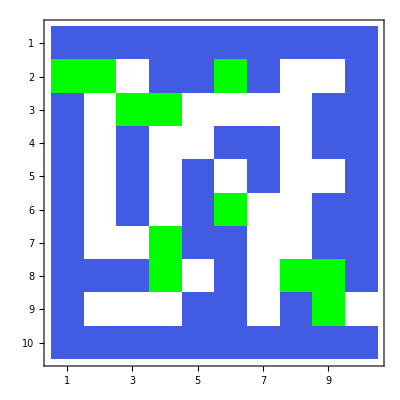

```mathematica
MatrixPlot[ReplacePart[labyrinth,Treats-> 5],{ColorRules->{5-> Green}}]
```

```mathematica
Manipulate[MatrixPlot[ReplacePart[labyrinth,{Intersection[pathForFood⟦1;;a⟧,Treats]-> 20,pathForFood⟦1;;a⟧->10,Treats-> 5}],{ColorRules->{5-> Green,10->Yellow,20-> Purple}}],{a,1,Length[pathForFood],1}]
```

```mathematica
save2[t_]:=MatrixPlot[ReplacePart[labyrinth,{Intersection[pathForFood⟦1;;t⟧,Treats]-> 20,pathForFood⟦1;;t⟧->10,Treats-> 5}],{ColorRules->{5-> Green,10->Yellow,20-> Purple}}]
(**Export["C:\\Users\\FullSpace\\Desktop\\courseWork\\solution2gif\\"<>ToString[#]<>".png",save2[#]]&/@Range[1,Length[pathForFood]];**)
```

## Поиск выхода для лабиринта из интернета

```mathematica
ImageOfLabirynth=Import["C:\\Users\\FullSpace\\Desktop\\courseWork\\labyrinth.jpg"]
```

-Graphics-

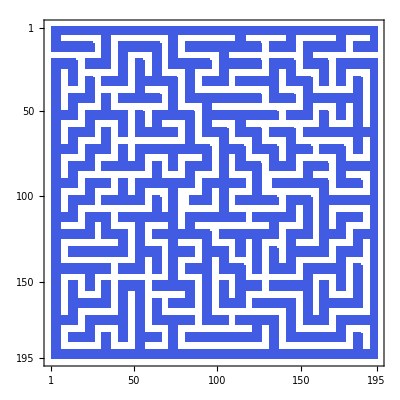

```mathematica
razreshenie={3,3};
labi2=(Round[Min[#]]-1)&/@ImageMeasurements[#,"Min"]&/@(ImagePartition[ImageOfLabirynth,razreshenie]);
MatrixPlot[%]
```

```mathematica
enterance=findEnterance[labi2];
exit=findExit[labi2];
```

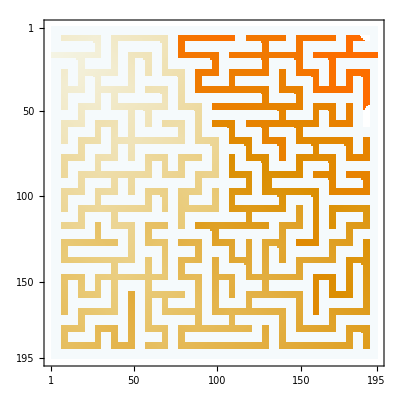

```mathematica
gridForLabi2=makeGrid[labi2,enterance,exit];
MatrixPlot[%]
```

```mathematica
solution2=findPath[gridForLabi2,enterance,exit];
Manipulate[MatrixPlot[ReplacePart[labi2,(solution2//Reverse)⟦1;;a⟧->10],ColorRules->{10->Red}],{a,1,Length[solution2],1}]
```

## Добавление “еды” для лабиринта из интернета.

```mathematica
enterance=findEnterance[labi2];
```

```mathematica
numberOfTreats = 10;
Treats = RandomSample[DeleteCases[Position[labi2, 0],enterance1], numberOfTreats];
Pheramones = Table[.5, {i, 1, numberOfTreats+1}, {j, 1, numberOfTreats+1}];
Treats=Prepend[Treats,enterance];
```

```mathematica
CreateGraphForTreat[labyrinth_,numberOfTreats_,Treats_,closenessconst_]:=Block[{TreatsDistancesRelatively,tempGrid,TreatsDistances},
TreatsDistancesRelatively=Table[0,{i,1,numberOfTreats},{j,1,numberOfTreats}];
TreatsDistances=Table[0,{i,1,numberOfTreats},{j,1,numberOfTreats}];
For[i=1,i≤ numberOfTreats,i++,
tempGrid=makeFullGrid[labyrinth,Treats⟦i⟧];
TreatsDistances⟦i⟧=Extract[tempGrid,Treats];
TreatsDistancesRelatively⟦i⟧=closenessconst/Extract[tempGrid,Treats];
];
{TreatsDistancesRelatively,TreatsDistances}
]
```

```mathematica
TreatsDistancesRelatively=CreateGraphForTreat[labi2,numberOfTreats+1,Treats,10];
TreatsDistances=TreatsDistancesRelatively//Last;
TreatsDistancesRelatively=TreatsDistancesRelatively//First;
```

```mathematica
a=1;(**можно сказать увеличивает зависимость выбора от дистанции**)
b=1;(**можно сказать увеличивает зависимость выбора от ферамонов**)
Q=20;(**константа при добавлении феромонов**)
p=.4;(**коэф испарения**)
numberOfGoldDiggers=10;(**amount of ants**)
```

```mathematica
bestpath=AntColony[Treats,TreatsDistances,TreatsDistancesRelatively,Pheramones,a,b,Q,p,numberOfGoldDiggers,100]
```

{1366,{1,3,10,9,2,5,4,6,7,8,11}}

```mathematica
DrawAntSolutionByPath[labyrinth_,Treats_,path_]:=Block[{connections,exit=findExit[labyrinth],pointscoordinates,res},
connections=MapThread[{Treats⟦#1⟧,Treats⟦#2⟧}&,{path//Most,RotateLeft[path]//Most}];
connections=Append[connections,{connections//Last//Last,exit}];
res=Reverse[firstAlgorithm[labyrinth,#//First,#//Last]]&/@connections;
res=Flatten[res,1];
res=res*MapThread[(#1==#2)/.{False-> 1,True-> 0}&,{res,RotateLeft[res]}];
DeleteCases[res,{0,0}]
]
pathForFood=DrawAntSolutionByPath[labi2,Treats,bestpath//Last];
```

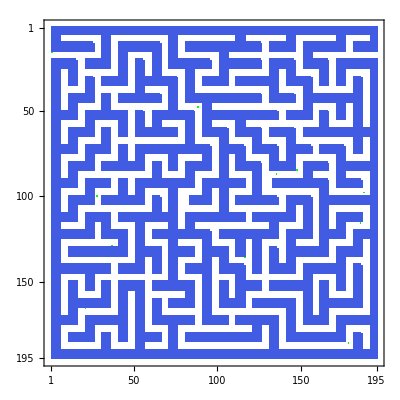

```mathematica
MatrixPlot[ReplacePart[labi2,Treats-> 5],{ColorRules->{5-> Green}}]
```

```mathematica
Manipulate[MatrixPlot[ReplacePart[labi2,{pathForFood⟦1;;a⟧->10,Treats-> 5,Intersection[pathForFood⟦1;;a⟧,Treats]-> 20}],{ColorRules->{5-> Green,10->Yellow,20-> Purple}}],{a,1,Length[pathForFood],1}]
```

```mathematica
save2[t_]:=MatrixPlot[ReplacePart[labyrinth,{Intersection[pathForFood⟦1;;t⟧,Treats]-> 20,pathForFood⟦1;;t⟧->10,Treats-> 5}],{ColorRules->{5-> Green,10->Yellow,20-> Purple}}]
(**Export["C:\\Users\\FullSpace\\Desktop\\courseWork\\solution2gif\\"<>ToString[#]<>".png",save2[#]]&/@Range[1,Length[pathForFood]];**)
```